The data for the costs of flights was calculated on Sat 4 Jun 2022 10:45:09 at Google Flights.

## ListPlot Different Labels

#### Callout

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Metric"]&)/@cities,{230,651,221,279,722,768,221,970,529,529}}]];
ListPlot[(Callout[travelAssociation[#1],#1["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[FontFamily->"JetBrains Mono"],ImageSize->Scaled[.8],Frame->True,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

-Graphics-

#### Tooltips

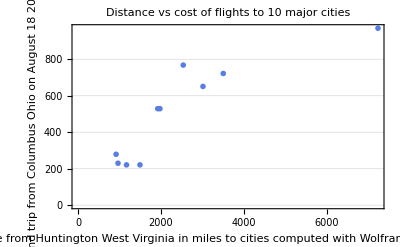

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Metric"]&)/@cities,{230,651,221,279,722,768,221,970,529,529}}]];
ListPlot[(Tooltip[travelAssociation[#1],#1["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[FontFamily->"JetBrains Mono"],Frame->True,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

#### Legend

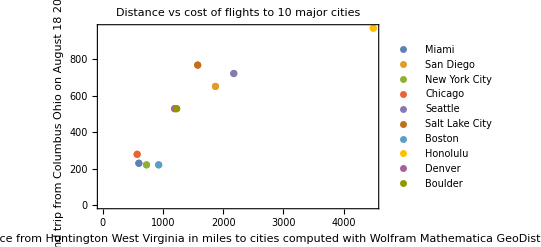

```mathematica
Module[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
travelAssociation=List/@AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Imperial"]&)/@cities,{230,651,221,279,722,768,221,970,529,529}}]];
ListPlot[(Legended[travelAssociation[#1],#["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[FontFamily->"JetBrains Mono"],ImageSize->Scaled[.87],Frame->True,PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

## Final Choice

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Imperial"]&)/@cities,{230,651,221,279,722,768,221,970,529,529}}]];
ListPlot[(Callout[travelAssociation[#1],#1["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[FontFamily->"JetBrains Mono"],ImageSize->Scaled[.8],Frame->True,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

-Graphics-

## Exporting the data to a PNG image file

```mathematica
Export["C:\\Users\\peter\\Documents\\Statistics Class Laura Stapleton Summer I\\scatterplot of flight distance in miles and cost on August 18 2022.png",Rasterize[Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Imperial"]&)/@cities,{230,651,221,279,722,768,221,970,529,529}}]];
ListPlot[(Callout[travelAssociation[#1],#1["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[FontFamily->"JetBrains Mono"],ImageSize->Scaled[.8],Frame->True,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]]]
```

C:\Users\peter\Documents\Statistics Class Laura Stapleton Summer I\scatterplot of flight distance in miles and cost on August 18 2022.png

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\Statistics Class Laura Stapleton Summer I\\scatterplot of flight distance in miles and cost on August 18 2022.png"]
```

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Imperial"]&)/@cities,{230,651,221,279,722,768,221,970,529,529}}]];Fit[Transpose[{(QuantityMagnitude@GeoDistance[Here,#1,UnitSystem->"Imperial"]&)/@cities,{230,651,221,279,722,768,221,970,529,529}}],{1,miles},miles]]
```

208.07+0.197823 miles

## TravelDistances

```mathematica
Table[GeoDistance[Here,city,UnitSystem->"Imperial"],{city,{Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]}}]
```

{599.252 mi,1871.86 mi,726.591 mi,570.806 mi,2175.78 mi,1576.43 mi,928.109 mi,4493.34 mi,1194.32 mi,1227.25 mi}

Rounding the travel distances

```mathematica
Table[Round@GeoDistance[Here,city,UnitSystem->"Imperial"],{city,{Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]}}]
```

{599 mi,1872 mi,727 mi,571 mi,2176 mi,1576 mi,928 mi,4493 mi,1194 mi,1227 mi}